# Examen parcial IV

## Pregunta 1

Sea 


Encuentra y clasifica todas las soluciones de equilibrio.

Solución:
Buscamos soluciones ,  para toda . Sustituimos en la primera ecuación y obtenemos


De la segunda ecuación obtenemos

Sustituyendo esta ecuación en la anterior obtenemos




Por lo que  y 
De la otra ecuación tenemos entonces que:
, 
Entonces los puntos de equilibrio son  y .
Calculamos la matriz Jacobiana del sistema

```mathematica
J1={{D[x^2-5*x+y,x],D[x^2-5*x+y,y]},{D[x^2,x],D[x^2,y]}};
TraditionalForm[MatrixForm[J1]]
```

(2 x-5 | 1
2 x | 0)

Primero evaluamos en el origen y calculamos los eigenvalores

```mathematica
Eigenvalues[J1/.{x->0,y->0}]
```

{-5,0}

Vemos que  pero , por lo que el punto de equilibrio atrae por una dirección y repele por otra, es un punto silla oscilatorio.
Ahora calculamos los eigenvalores del

```mathematica
Eigenvalues[J1/.{x->3,x->9}]
```

{3,-2}

En este caso,  y , por lo que repele a lo largo de ambas direcciones, por lo tanto es un punto de equilibrio inestable (similar a una espiral estable, pero con un eigenvalor negativo, en lugar de eigenvalores complejos).

## Pregunta 2

El método de Newton para encontrar numéricamente las raíces de una función  consiste en iterar la ecuación en diferencias finitas

Escribe la ecuación en diferencias con , muestra que la ecuación tiene dos puntos de equilibrio superestables, , y encuentra las soluciones numéricas con

La ecuación sería 

Las soluciones de equilibrio se dan cuando . Sustituyendo, obtenemos




Para la estabilidad, calculamos la derivada del lado derecho y evaluamos en los puntos de equilibrio:






Por lo tanto son superestables. Vemos la solución con condición inicial

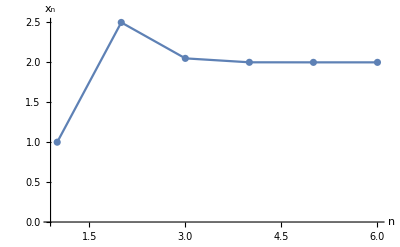

```mathematica
sol1=RecurrenceTable[{x[n+1]==x[n]-(x[n]^2-4)/(2*x[n]),x[0]==1},x,{n,0,5}];
ListPlot[sol1,Joined->True,Mesh->All,PlotRange->All,AxesLabel->{n,Subscript[x,n]}]
```

Demuestra que, para toda función , las raíces  son puntos de equilibrio superestables de la ecuación en diferencias del método de Newton.

Suponemos que existe  tal que . Ahora, tomamos la condición inicial , y calculamos la solución  iterando.
 


Donde usamos que  por ser raíz, y supusimos que 
Vemos que  para  y por lo tanto para cualquier otra , por lo que  es solución de equilibrio. Ahora calculamos la estabilidad calculando el lado derecho de la ecuación.







donde usamos   por ser raíz, y supusimos que . Por lo tanto, las raíces son puntos de equilibrio superestables de la ecuación en diferencias, pero el método podría tener problemas cuando  además de ser una raíz también es un punto crítico.

## Pregunta 3

Considera el sistema en coordenadas polares


Usando el mapeo de Poincaré generado por la sección de Poincaré , muestra que existe un único ciclo límite y determina su estabilidad.

Solución:
Vemos que el sistema está desacoplado y el ángulo crece como , salvo una constante, por lo que las soluciones giran a la derecha y llegan a un punto con el mismo ángulo después de un tiempo de . Vemos que la sección  puede verse como todos aquellos puntos con , por lo que una solución que intersecta a  en , intersecta en  en un tiempo igual a . Por lo tanto, tenemos la siguiente relación

Usando la relga de la cadena tenemos que ,  y por el teorema de la función implícita, tenemos que , y recordando que  por la primera ecuación diferencial, sustituyendo en la integral obtenemos

Usando fracciones parciales podemos llegar a que , sustituyendo:



Donde usamos las propiedades del logaritmo. Despejamos los términos con :










Sabemos que en el mapeo de Poincaré, los ciclos límite corresponden a puntos de equilibrio, por lo que buscamos soluciones . Sustituimos en la ecuación anterior para obtener:

Inmediatamente vemos que la igualdad se cumple para . Sin embargo, esto no es un ciclo límite, ya que una solución que cruce en  es una solución radial con radio cero, lo cual corresponde al punto de equilibrio del origen. Si no es cero, entonces dividimos de ambos lados y obtenemos:





Este sí es un ciclo límite, puesto que una trayectoria con radio uno es un círculo. Ahora determinamos la estabilidad de este ciclo límite con la estabilidad del punto de equilibrio . Para esto, derivamos el lado derecho de la ecuación, lo evaluamos en el punto de equilibrio, y vemos si, en valor absoluto, es menor a uno:





Por lo tanto, es estable.

```mathematica
Solve[(-1-r)^2 x+(-r-r^2) x^2+2 (1+3 r+3 r^2+r^3) x^3==0,x]
```

{{x→0},{x→(r+r^2-√(-8-40 r-79 r^2-78 r^3-39 r^4-8 r^5))/(4 (1+3 r+3 r^2+r^3))},{x→(r+r^2+√(-8-40 r-79 r^2-78 r^3-39 r^4-8 r^5))/(4 (1+3 r+3 r^2+r^3))}}

## Pregunta 4

Sea

Calcula la estabilidad del punto de equilibrio , y demuestra que existe una bifurcación de flip en .

Para la estabilidad, calculamos la derivada







Vemos que hay pérdida de estabilidad del punto de equilibrio en . Para saber que la bifurcación es de flip, tenemos que ver que la derivada es negativa y disminuye de mayor a -1 a menor a -1. Entonces vemos cómo es la derivada para números positivos:



Por lo tanto, cuando , la derivada es menor a -1 y el punto de equlibrio es inestable, y cuando  (pero cerca de cero), la derivada es negativa pero mayor a -1 por lo que es estable, y hay una bifurcación de flip.

Usando la serie de Taylor del segundo iterado hasta orden tres, muestra que hay un ciclo límite de periodo dos para , que coalesce con el punto de equilibrio en . Argumenta porqué esto indica que hay una bifurcación de flip subcrítica.

Definimos el lado derecho de la ecuación:

```mathematica
f[x_,r_]:=-(1+r)*x-x^2-2*x^3;
```

Y expandimos su segundo iterado hasta tercer orden:

```mathematica
Series[f[f[x,r],r],{x,0,3}]
```

(-1-r)^2 x+(-r-r^2) x^2+2 (1+3 r+3 r^2+r^3) x^3+O[x]^4

Calculamos las soluciones de equilibrio del segundo iterado como

```mathematica
Solve[x==(-1-r)^2 x+(-r-r^2) x^2+2 (1+3 r+3 r^2+r^3) x^3,x]
```

{{x→0},{x→(r+r^2-√(-16 r-55 r^2-70 r^3-39 r^4-8 r^5))/(4 (1+3 r+3 r^2+r^3))},{x→(r+r^2+√(-16 r-55 r^2-70 r^3-39 r^4-8 r^5))/(4 (1+3 r+3 r^2+r^3))}}

Obtenemos el punto de equilibrio orignal, más otros dos puntos de equilibrio que corresponden al ciclo de período dos. Podemos ver que, cuando , estas soluciones son complejas, por lo que sólo existen cuando . Cuando , vemos que ambos puntos del ciclo coinciden con la solución de equilibrio, puesto que todo está muliplicado por  en el numerador. Mostramos anteriormente que cuando  el punto de equilibrio es estable. Como en este régimen existe el ciclo, concluimos que debe ser de flip subcrítico (en las bifucarciones supercríticas, el ciclo existe cuando el punto de equilibrio es inestable, y en el caso subcrítico, el ciclo existe cuando el punto de equilibrio es estable). 
Opcionalmente podemos obtener el diagrama de bifurcación y examinar las soluciones numéricas para comprobar que el ciclo es inestable:
En la aproximación:

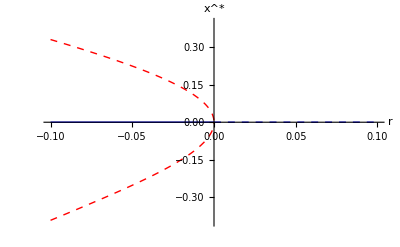

```mathematica
Show[{Plot[0,{x,-0.1,0},PlotStyle->{Blue,Thick},AxesLabel->{r,SuperStar[x]},PlotRange->{{-0.1,0.1},{-0.4,0.4}}],Plot[0,{x,0,0.1},PlotStyle->{Blue,Thick,Dashed}],Plot[(r+r^2-√(-16 r-55 r^2-70 r^3-39 r^4-8 r^5))/(4 (1+3 r+3 r^2+r^3)),{r,-0.1,0},PlotStyle->{Red,Thick,Dashed}],Plot[(r+r^2+√(-16 r-55 r^2-70 r^3-39 r^4-8 r^5))/(4 (1+3 r+3 r^2+r^3)),{r,-0.1,0},PlotStyle->{Red,Thick,Dashed}]}]
```

En el sistema no lineal completo:

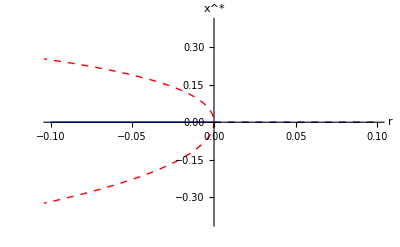

```mathematica
cyc1=ParallelTable[{r,x/.FindRoot[x==f[f[x,r],r],{x,1}]},{r,-1,0,0.0001}];
cyc2=ParallelTable[{r,x/.FindRoot[x==f[f[x,r],r],{x,-1}]},{r,-1,0,0.0001}];
Show[{Plot[0,{x,-0.1,0},PlotStyle->{Blue,Thick},AxesLabel->{r,SuperStar[x]},PlotRange->{{-0.1,0.1},{-0.4,0.4}}],Plot[0,{x,0,0.1},PlotStyle->{Blue,Thick,Dashed}],ListPlot[cyc1,Joined->True,PlotStyle->{Red,Thick,Dashed}],ListPlot[cyc2,Joined->True,PlotStyle->{Red,Thick,Dashed}]}]
```

Una solución después de la bifurcación:

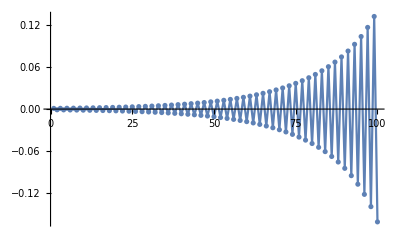

```mathematica
sol2=RecurrenceTable[{x[n+1]==f[x[n],0.05],x[1]==0.001},x,{n,1,100}];
ListPlot[sol2,Joined->True,Mesh->All,PlotRange->All]
```

Una solución antes de la bifurcación dentro del ciclo inestable:

```mathematica
cyc1[[9500]]
```

{-0.0501,0.189383}

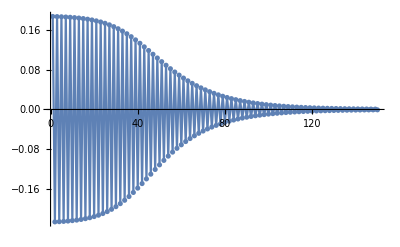

```mathematica
sol3=RecurrenceTable[{x[n+1]==f[x[n],-0.05],x[1]==0.188},x,{n,1,150}];
ListPlot[sol3,Joined->True,Mesh->All,PlotRange->All]
```

Una solución antes de la bifurcación fuera del ciclo inestable:

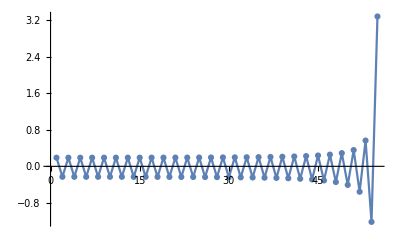

```mathematica
sol4=RecurrenceTable[{x[n+1]==f[x[n],-0.05],x[1]==0.1895},x,{n,1,55}];
ListPlot[sol4,Joined->True,Mesh->All,PlotRange->All]
```